# The Continuous Space Signature of Phenotypic Coevolution

Bob Week
Feb 24, 2021

## Computing the Power Spectrum (ie, the Fourier Transform of the Cov fct)

```mathematica
ℋ={{Subscript[b, H](Subscript[κ, H]^2+(Subscript[k, 1]^2+Subscript[k, 2]^2))^(Subscript[α, H]/2),Subscript[b, HP](Subscript[κ, HP]^2+(Subscript[k, 1]^2+Subscript[k, 2]^2))^(Subscript[α, HP]/2)},{Subscript[b, PH](Subscript[κ, PH]^2+(Subscript[k, 1]^2+Subscript[k, 2]^2))^(Subscript[α, PH]/2),Subscript[b, P](Subscript[κ, P]^2+(Subscript[k, 1]^2+Subscript[k, 2]^2))^(Subscript[α, P]/2)}};
Subscript[S, V]={{Subscript[σ, H]^2,0},{0,Subscript[σ, P]^2}};
MatrixForm[ℋ]
MatrixForm[Subscript[S, V]]
```

(b_H (k_1^2+k_2^2+κ_H^2)^(α_H/2) | b_HP (k_1^2+k_2^2+κ_HP^2)^(α_HP/2)
b_PH (k_1^2+k_2^2+κ_PH^2)^(α_PH/2) | b_P (k_1^2+k_2^2+κ_P^2)^(α_P/2))

(σ_H^2 | 0
0 | σ_P^2)

```mathematica
Subscript[ℋ, s]=ℋ/.{Subscript[α, HP]->0,Subscript[α, PH]->0}
```

{{b_H (k_1^2+k_2^2+κ_H^2)^(α_H/2),b_HP},{b_PH,b_P (k_1^2+k_2^2+κ_P^2)^(α_P/2)}}

```mathematica
Subscript[S, ζ]=Simplify[Inverse[Subscript[ℋ, s]].Subscript[S, V].Transpose[Inverse[Subscript[ℋ, s]]]];
MatrixForm[Subscript[S, ζ]]
```

((b_P^2 (k_1^2+k_2^2+κ_P^2)^α_P σ_H^2+b_HP^2 σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2)^(α_H/2) (k_1^2+k_2^2+κ_P^2)^(α_P/2))^2) | -(b_P b_PH (k_1^2+k_2^2+κ_P^2)^(α_P/2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2)^(α_H/2) σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2)^(α_H/2) (k_1^2+k_2^2+κ_P^2)^(α_P/2))^2)
-(b_P b_PH (k_1^2+k_2^2+κ_P^2)^(α_P/2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2)^(α_H/2) σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2)^(α_H/2) (k_1^2+k_2^2+κ_P^2)^(α_P/2))^2) | (b_PH^2 σ_H^2+b_H^2 (k_1^2+k_2^2+κ_H^2)^α_H σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2)^(α_H/2) (k_1^2+k_2^2+κ_P^2)^(α_P/2))^2))

```mathematica
Integrate[Subscript[S, ζ][[1,2]],{Subscript[k, 1],-∞,+∞},{Subscript[k, 2],-∞,+∞}]
```

$Aborted

Weak coupling approximation

```mathematica
Subscript[Ŝ, ζ]=Subscript[S, ζ]/.{Subscript[b, HP]^2->0,Subscript[b, PH]^2->0,Subscript[b, HP] Subscript[b, PH]->0}
```

{{((k_1^2+k_2^2+κ_H^2)^-α_H σ_H^2)/b_H^2,-((k_1^2+k_2^2+κ_H^2)^-α_H (k_1^2+k_2^2+κ_P^2)^-α_P (b_P b_PH (k_1^2+k_2^2+κ_P^2)^(α_P/2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2)^(α_H/2) σ_P^2))/(b_H^2 b_P^2)},{-((k_1^2+k_2^2+κ_H^2)^-α_H (k_1^2+k_2^2+κ_P^2)^-α_P (b_P b_PH (k_1^2+k_2^2+κ_P^2)^(α_P/2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2)^(α_H/2) σ_P^2))/(b_H^2 b_P^2),((k_1^2+k_2^2+κ_P^2)^-α_P σ_P^2)/b_P^2}}

```mathematica
Expand[Subscript[Ŝ, ζ][[1,2]]]
```

-(b_PH (k_1^2+k_2^2+κ_H^2)^-α_H (k_1^2+k_2^2+κ_P^2)^(-α_P/2) σ_H^2)/(b_H^2 b_P)-(b_HP (k_1^2+k_2^2+κ_H^2)^(-α_H/2) (k_1^2+k_2^2+κ_P^2)^-α_P σ_P^2)/(b_H b_P^2)

```mathematica
FullSimplify[InverseFourierTransform[Subscript[Ŝ, ζ][[1,1]],{Subscript[k, 1],Subscript[k, 2]},{Subscript[x, 1],Subscript[x, 2]}]]
```

(2^(1-α_11) BesselK[-1+α_11,(√(x_1^2+x_2^2))/(√(1/κ_11^2))] (x_1^2+x_2^2)^(1/2 (-1+α_11)) (1/κ_11^2)^(1/2-α_11/2) (κ_11^2)^(1-α_11) σ_n1^2)/(Gamma[α_11] b_11^2)

```mathematica
Integrate[(2^(1-Subscript[α, 11]) BesselK[-1+Subscript[α, 11],(√(Subscript[x, 1]^2+Subscript[x, 2]^2))/(√(1/Subscript[κ, 11]^2))] (Subscript[x, 1]^2+Subscript[x, 2]^2)^(1/2 (-1+Subscript[α, 11])) (1/Subscript[κ, 11]^2)^(1/2-Subscript[α, 11]/2) (Subscript[κ, 11]^2)^(1-Subscript[α, 11]) Subscript[σ, n1]^2)/(Gamma[Subscript[α, 11]] Subscript[b, 11]^2),{Subscript[x, 1],-∞,+∞},{Subscript[x, 2],-∞,+∞}]
```

$Aborted

```mathematica
FullSimplify[InverseFourierTransform[Expand[Subscript[Ŝ, ζ][[1,2]]],{Subscript[k, 1],Subscript[k, 2]},{Subscript[x, 1],Subscript[x, 2]}]]
```

$Aborted

```mathematica
Integrate[Subscript[Ŝ, ζ][[1,1]],{Subscript[k, 1],-∞,+∞},{Subscript[k, 2],-∞,+∞}]
```

ConditionalExpression[(π (κ_11^2)^(1-α_11) σ_n1^2)/(b_11^2 (-1+α_11)), Re[α_11]>1&&Re[κ_11^2]>0]

```mathematica
Integrate[Subscript[Ŝ, ζ][[1,2]],{Subscript[k, 1],-∞,+∞},{Subscript[k, 2],-∞,+∞}]
```

```mathematica
ConditionalExpression[-(π (Subscript[κ, 11]^2)^(-Subscript[α, 11]) (Subscript[κ, 22]^2)^(-Subscript[α, 22]) ((2 Hypergeometric2F1[1,Subscript[α, 11],2-Subscript[α, 22]/2,Subscript[κ, 22]^2/Subscript[κ, 11]^2] Subscript[b, 21] Subscript[b, 22] (Subscript[κ, 22]^2)^(1+Subscript[α, 22]/2) Subscript[σ, n1]^2)/(-2+Subscript[α, 22])+(π Csc[(π Subscript[α, 22])/2] Gamma[-1+Subscript[α, 11]+Subscript[α, 22]/2] Subscript[b, 21] Subscript[b, 22] (1/Subscript[κ, 11]^2)^(-1+Subscript[α, 22]/2) (1/Subscript[κ, 22]^2)^(-Subscript[α, 22]/2) (Subscript[κ, 22]^2)^(Subscript[α, 22]/2) (1-Subscript[κ, 22]^2/Subscript[κ, 11]^2)^(1-Subscript[α, 11]-Subscript[α, 22]/2) Subscript[σ, n1]^2)/(Gamma[Subscript[α, 11]] Gamma[Subscript[α, 22]/2])+(Hypergeometric2F1[1,Subscript[α, 11]/2,2-Subscript[α, 22],Subscript[κ, 22]^2/Subscript[κ, 11]^2] Subscript[b, 11] Subscript[b, 12] (Subscript[κ, 11]^2)^(Subscript[α, 11]/2) Subscript[κ, 22]^2 Subscript[σ, n2]^2)/(-1+Subscript[α, 22])+(π Csc[π Subscript[α, 22]] Gamma[-1+Subscript[α, 11]/2+Subscript[α, 22]] Subscript[b, 11] Subscript[b, 12] (1/Subscript[κ, 11]^2)^Subscript[α, 22] (Subscript[κ, 11]^2)^(1+Subscript[α, 11]/2) (1/Subscript[κ, 22]^2)^(-Subscript[α, 22]) (1-Subscript[κ, 22]^2/Subscript[κ, 11]^2)^(1-Subscript[α, 11]/2-Subscript[α, 22]) Subscript[σ, n2]^2)/(Gamma[Subscript[α, 11]/2] Gamma[Subscript[α, 22]])))/(Subscript[b, 11]^2 Subscript[b, 22]^2), Re[Subscript[α, 11]+Subscript[α, 22]/2]>1&&Re[Subscript[α, 11]/2+Subscript[α, 22]]>1&&Re[Subscript[κ, 11]^2]>0&&Re[Subscript[κ, 22]^2]>0]
```

```mathematica
Integrate[Subscript[Ŝ, ζ][[1,2]]/.{Subscript[α, H]->2,Subscript[α, P]->2},{Subscript[k, 1],-∞,+∞},{Subscript[k, 2],-∞,+∞}]
```

```mathematica
ConditionalExpression[-(π (Subscript[b, P] Subscript[b, PH] Subscript[κ, P]^2 ((-1+Log[Subscript[κ, H]^2]-Log[Subscript[κ, P]^2]) Subscript[κ, H]^2+Subscript[κ, P]^2) Subscript[σ, H]^2+Subscript[b, H] Subscript[b, HP] Subscript[κ, H]^2 (Subscript[κ, H]^2+(-1-Log[Subscript[κ, H]^2]+Log[Subscript[κ, P]^2]) Subscript[κ, P]^2) Subscript[σ, P]^2))/(Subscript[b, H]^2 Subscript[b, P]^2 Subscript[κ, H]^2 Subscript[κ, P]^2 (Subscript[κ, H]^2-Subscript[κ, P]^2)^2), Re[Subscript[κ, H]]≠0&&Re[Subscript[κ, P]]≠0&&((Re[Subscript[κ, P]^2]≥0&&Subscript[κ, P]≠0)||Subscript[κ, P]^2∉Reals)&&((Re[Subscript[κ, H]^2]≥0&&Subscript[κ, H]≠0)||Subscript[κ, H]^2∉Reals)]
```

```mathematica
Subscript[Ĉ, HP,0]=Apart[-1/(Subscript[b, H]^2 Subscript[b, P]^2 Subscript[κ, H]^2 Subscript[κ, P]^2 (Subscript[κ, H]^2-Subscript[κ, P]^2)^2)(Subscript[b, P] Subscript[b, PH] Subscript[κ, P]^2 ((-1+Log[Subscript[κ, H]^2]-Log[Subscript[κ, P]^2]) Subscript[κ, H]^2+Subscript[κ, P]^2) Subscript[σ, H]^2+Subscript[b, H] Subscript[b, HP] Subscript[κ, H]^2 (Subscript[κ, H]^2+(-1-Log[Subscript[κ, H]^2]+Log[Subscript[κ, P]^2]) Subscript[κ, P]^2) Subscript[σ, P]^2)]
```

-(b_PH (-κ_H^2+Log[κ_H^2] κ_H^2-Log[κ_P^2] κ_H^2+κ_P^2) σ_H^2)/(b_H^2 b_P κ_H^2 (κ_H-κ_P)^2 (κ_H+κ_P)^2)-(b_HP (κ_H^2-κ_P^2-Log[κ_H^2] κ_P^2+Log[κ_P^2] κ_P^2) σ_P^2)/(b_H b_P^2 (κ_H-κ_P)^2 κ_P^2 (κ_H+κ_P)^2)

```mathematica
Subscript[Ŝ, ζ,12,0]=Subscript[Ŝ, ζ][[1,2]]/.{Subscript[α, H]->2,Subscript[α, P]->2,Subscript[k, 1]->0,Subscript[k, 2]->0}
```

-(b_P b_PH κ_P^2 σ_H^2+b_H b_HP κ_H^2 σ_P^2)/(b_H^2 b_P^2 κ_H^4 κ_P^4)

#### Computing Integral Range of Interspecific Trait Covariance

```mathematica
Subscript[l, HP]=Sqrt[FullSimplify[Subscript[Ŝ, ζ,12,0]/Subscript[Ĉ, HP,0]]]
```

√(((κ_H^2-κ_P^2)^2 (b_P b_PH κ_P^2 σ_H^2+b_H b_HP κ_H^2 σ_P^2))/(b_P b_PH κ_H^2 κ_P^4 ((-1+Log[κ_H^2]-Log[κ_P^2]) κ_H^2+κ_P^2) σ_H^2+b_H b_HP κ_H^4 κ_P^2 (κ_H^2+(-1-Log[κ_H^2]+Log[κ_P^2]) κ_P^2) σ_P^2))

```mathematica
Subscript[l, HP,C]=FullSimplify[ExpandAll[Subscript[l, HP]/.subs]]
```

1/(√2)(√((((-A_H+B_H) d_P G_H+(A_P+B_P) d_H G_P)^2 ((A_H-B_H) B_H G_H n_H-B_P (A_P+B_P) G_P n_P))/((A_H-B_H) (A_P+B_P) G_H G_P (A_H^2 B_H d_P G_H^2 n_H+B_H^2 G_H (B_H d_P G_H+(1+Log[((A_H-B_H) G_H)/d_H]-Log[((A_P+B_P) G_P)/d_P]) (A_P+B_P) d_H G_P) n_H-B_P (A_P+B_P) G_P ((1-Log[((A_H-B_H) G_H)/d_H]+Log[((A_P+B_P) G_P)/d_P]) B_H d_P G_H+(A_P+B_P) d_H G_P) n_P+A_H G_H (-B_H (2 B_H d_P G_H+(1+Log[((A_H-B_H) G_H)/d_H]-Log[((A_P+B_P) G_P)/d_P]) (A_P+B_P) d_H G_P) n_H-(-1+Log[((A_H-B_H) G_H)/d_H]-Log[((A_P+B_P) G_P)/d_P]) B_P (A_P+B_P) d_P G_P n_P)))))

When background parameters are the same

```mathematica
Plot3D[Subscript[l, HP,C]/.{Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[B, H]->0.01,Subscript[B, P]->0.01,Subscript[n, H]->1000,Subscript[n, P]->1000},{Subscript[d, H],0.01,10},{Subscript[d, P],0.01,10},AxesLabel->Automatic]
```

-Graphics3D-

When host selection is stronger than parasite selection

```mathematica
Plot3D[Subscript[l, HP,C]/.{Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[B, H]->0.02,Subscript[B, P]->0.01,Subscript[n, H]->1000,Subscript[n, P]->1000},{Subscript[d, H],0.01,10},{Subscript[d, P],0.01,10},AxesLabel->Automatic]
```

-Graphics3D-

When parasite selection is stronger than host selection

```mathematica
Plot3D[Subscript[l, HP,C]/.{Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[B, H]->0.01,Subscript[B, P]->0.02,Subscript[n, H]->1000,Subscript[n, P]->1000},{Subscript[d, H],0.01,10},{Subscript[d, P],0.01,10},AxesLabel->Automatic]
```

-Graphics3D-

When host evolvability is higher than parasite evolvability

```mathematica
Plot3D[Subscript[l, HP,C]/.{Subscript[G, H]->20,Subscript[G, P]->10,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[B, H]->0.01,Subscript[B, P]->0.01,Subscript[n, H]->1000,Subscript[n, P]->1000},{Subscript[d, H],0.01,10},{Subscript[d, P],0.01,10},AxesLabel->Automatic]
```

-Graphics3D-

When parasite evolvability is higher than host evolvability

```mathematica
Plot3D[Subscript[l, HP,C]/.{Subscript[G, H]->10,Subscript[G, P]->20,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[B, H]->0.01,Subscript[B, P]->0.01,Subscript[n, H]->1000,Subscript[n, P]->1000},{Subscript[d, H],0.01,10},{Subscript[d, P],0.01,10},AxesLabel->Automatic]
```

-Graphics3D-

As function of strengths of biotic selection

```mathematica
Plot3D[Subscript[l, HP,C]/.{Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[d, H]->10,Subscript[d, P]->10,Subscript[n, H]->1000,Subscript[n, P]->1000},{Subscript[B, H],0,0.075},{Subscript[B, P],0,0.075},AxesLabel->Automatic]
```

-Graphics3D-

## Directly taking Fourier inverse of above matrix is going nowhere. Try reconstructing it.

```mathematica
M[x_,y_,κ_,ν_]:=2^(1-ν)/Gamma[ν](κ √(x^2+y^2))^ν BesselK[ν,κ √(x^2+y^2)];
```

#### Converting to Meijer G forms

```mathematica
MeijerGReduce[M[Subscript[x, 1],Subscript[x, 2],κ,1],√(Subscript[x, 1]^2+Subscript[x, 2]^2)]
```

1/2 κ √(x_1^2+x_2^2) MeijerG[{{},{}},{{1/2,-1/2},{}},1/2 κ √(x_1^2+x_2^2),1/2]

```mathematica
MeijerGReduce[M[Subscript[x, 1],Subscript[x, 2],κ,2],√(Subscript[x, 1]^2+Subscript[x, 2]^2)]
```

1/4 κ^2 (x_1^2+x_2^2) MeijerG[{{},{}},{{1,-1},{}},1/2 κ √(x_1^2+x_2^2),1/2]

```mathematica
MeijerGReduce[M[Subscript[x, 1],Subscript[x, 2],κ,3],√(Subscript[x, 1]^2+Subscript[x, 2]^2)]
```

1/16 κ^3 (x_1^2+x_2^2)^(3/2) MeijerG[{{},{}},{{3/2,-3/2},{}},1/2 κ √(x_1^2+x_2^2),1/2]

```mathematica
FourierTransform[M[Subscript[x, 1],Subscript[x, 2],κ,1/4],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]
```

$Aborted

## Coevolutionary Parameters

```mathematica
Element[Subscript[d, H],Reals];
Element[Subscript[G, H],Reals];
Element[Subscript[B, H],Reals];
Element[Subscript[A, H],Reals];
Element[Subscript[n, H],Reals];
Element[Subscript[d, P],Reals];
Element[Subscript[G, P],Reals];
Element[Subscript[B, P],Reals];
Element[Subscript[A, P],Reals];
Element[Subscript[n, P],Reals];
```

```mathematica
subs={Subscript[σ, H]-> √(Subscript[G, H]/Subscript[n, H]),Subscript[σ, P]-> √(Subscript[G, P]/Subscript[n, P]),Subscript[α, H]->2,Subscript[α, P]->2,Subscript[κ, H]->√((Subscript[G, H](Subscript[A, H]-Subscript[B, H]))/(Subscript[d, H]/2)),Subscript[κ, P]->√((Subscript[G, P](Subscript[A, P]+Subscript[B, P]))/(Subscript[d, P]/2)),Subscript[b, H]->Subscript[d, H]/2,Subscript[b, P]->Subscript[d, P]/2,Subscript[b, HP]->Subscript[G, H] Subscript[B, H],Subscript[b, PH]->-Subscript[G, P] Subscript[B, P]}
```

{σ_H→√(G_H/n_H),σ_P→√(G_P/n_P),α_H→2,α_P→2,κ_H→√2 √(((A_H-B_H) G_H)/d_H),κ_P→√2 √(((A_P+B_P) G_P)/d_P),b_H→d_H/2,b_P→d_P/2,b_HP→B_H G_H,b_PH→-B_P G_P}

```mathematica
MatrixForm[Subscript[S, ζ]/.subs]
```

(((d_P^2 G_H ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2)^2)/(4 n_H)+(B_H^2 G_H^2 G_P)/n_P)/((-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2) | -(-(B_P d_P G_H G_P ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))/(2 n_H)+(B_H d_H G_H G_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2))/(2 n_P))/((-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2)
-(-(B_P d_P G_H G_P ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))/(2 n_H)+(B_H d_H G_H G_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2))/(2 n_P))/((-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2) | ((B_P^2 G_H G_P^2)/n_H+(d_H^2 G_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2)^2)/(4 n_P))/((-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2))

## Use Weak Selection Approximation

First try just weak biotic selection (B_H B_P,B_H^2,B_P^2~0)

```mathematica
Subscript[S, ζS]=FullSimplify[Subscript[S, ζ]/.subs/.{Subscript[B, H]->ϵ Subscript[B, H],Subscript[B, P]->ϵ Subscript[B, P]}/.{ϵ^2-> 0,ϵ^3->0,ϵ^4->0}/.{ϵ->1}];
MatrixForm[Subscript[S, ζS]]
```

((4 G_H)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 n_H) | (8 G_H G_P (-B_H (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) n_H+B_P (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_P))/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_H n_P)
(8 G_H G_P (-B_H (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) n_H+B_P (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_P))/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_H n_P) | (4 G_P)/((2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P))

```mathematica
Subscript[Ŝ, ζS,12]=Subscript[S, ζS][[1,2]]/(Subscript[S, ζS][[1,2]]/.{Subscript[k, 1]->0,Subscript[k, 2]->0})
```

(16 (A_H-B_H)^2 (A_P+B_P)^2 G_H^2 G_P^2 (-B_H (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) n_H+B_P (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_P))/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 (-2 (A_H-B_H) B_H G_H n_H+2 B_P (A_P+B_P) G_P n_P))

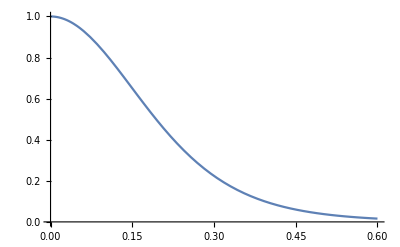

```mathematica
Plot[Subscript[Ŝ, ζS,12]/.{Subscript[k, 1]^2+Subscript[k, 2]^2->x^2}/.{Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[B, H]->0.01,Subscript[B, P]->0.01,Subscript[d, H]->10,Subscript[d, P]->10,Subscript[n, H]->1000,Subscript[n, P]->1000},{x,0,.6}]
```

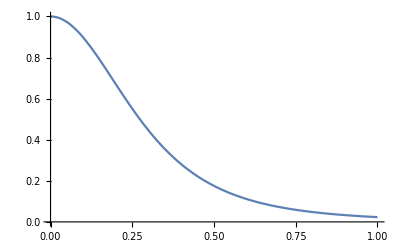

```mathematica
Plot[((Subscript[S, ζS][[1,1]]/.{Subscript[k, 1]^2+Subscript[k, 2]^2->x^2})/(Subscript[S, ζS][[1,1]]/.{Subscript[k, 1]->0,Subscript[k, 2]->0}))/.{Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.1,Subscript[A, P]->0.1,Subscript[B, H]->0.01,Subscript[B, P]->0.01,Subscript[d, H]->10,Subscript[d, P]->10,Subscript[n, H]->1000,Subscript[n, P]->1000},{x,0,1}]
```

The marginals are easy (Matern functions with smoothness par = 1)

```mathematica
FullSimplify[1/(Subscript[n, H] Subscript[d, H](Subscript[A, H]-Subscript[B, H]))FourierTransform[M[Subscript[x, 1],Subscript[x, 2],κ,1],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{κ->√((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H]))}]
```

(4 G_H)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 n_H)

```mathematica
FullSimplify[1/(Subscript[n, P] Subscript[d, P](Subscript[A, P]+Subscript[B, P]))FourierTransform[M[Subscript[x, 1],Subscript[x, 2],κ,1],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{κ->√((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}]
```

(4 G_P)/((2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P)

```mathematica
Subscript[C, 11]=FullSimplify[1/(Subscript[n, H] Subscript[d, H](Subscript[A, H]-Subscript[B, H]))M[Subscript[x, 1],Subscript[x, 2],κ,1]/.{κ->√((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H]))}];
Subscript[C, 22]=FullSimplify[1/(Subscript[n, P] Subscript[d, P](Subscript[A, P]+Subscript[B, P]))M[Subscript[x, 1],Subscript[x, 2],κ,1]/.{κ->√((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}];
Subscript[C, 12]=0;
```

```mathematica
MatrixForm[{{Subscript[C, 11],Subscript[C, 12]},{Subscript[C, 12],Subscript[C, 22]}}]
```

((√2 BesselK[1,√2 √(((A_H-B_H) G_H)/d_H) √(x_1^2+x_2^2)] G_H √(x_1^2+x_2^2))/(d_H^2 √(((A_H-B_H) G_H)/d_H) n_H) | 0
0 | (√2 BesselK[1,√2 √(((A_P+B_P) G_P)/d_P) √(x_1^2+x_2^2)] G_P √(x_1^2+x_2^2))/(d_P^2 √(((A_P+B_P) G_P)/d_P) n_P))

From this we see the marginal variances decrease with effective sizes, dispersal, and strengths of selection

Now let’s dive into the transformed cross-covariances...

```mathematica
Subscript[S, ζ12,1]=(8 Subscript[G, H] Subscript[G, P] (-Subscript[B, H] (2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2)) Subscript[n, H]))/((2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 Subscript[n, H] Subscript[n, P])
```

-(8 B_H G_H G_P)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P)

```mathematica
Subscript[S, ζ12,2]=(8 Subscript[G, H] Subscript[G, P] (Subscript[B, P] (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2)) Subscript[n, P]))/((2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 Subscript[n, H] Subscript[n, P])
```

(8 B_P G_H G_P)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_H)

These (^) are looking a lot like the F-transforms of convolutions of K_0 and Matern smooth-1 functions...

```mathematica
FullSimplify[(2 Subscript[G, H] Subscript[B, H])/(Subscript[n, P] Subscript[d, H] Subscript[d, P](Subscript[A, P]+Subscript[B, P]))FourierTransform[BesselK[0,Subscript[κ, 1] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]*FourierTransform[Subscript[κ, 2] √(Subscript[x, 1]^2+Subscript[x, 2]^2)BesselK[1,Subscript[κ, 2] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{Subscript[κ, 1]-> √((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H])),Subscript[κ, 2]-> √((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}]
```

(8 B_H G_H G_P)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P)

```mathematica
FullSimplify[(2 Subscript[G, P] Subscript[B, P])/(Subscript[n, H] Subscript[d, H] Subscript[d, P](Subscript[A, H]-Subscript[B, H]))FourierTransform[BesselK[0,Subscript[κ, 2] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]*FourierTransform[Subscript[κ, 1] √(Subscript[x, 1]^2+Subscript[x, 2]^2)BesselK[1,Subscript[κ, 1] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{Subscript[κ, 1]-> √((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H])),Subscript[κ, 2]-> √((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}]
```

(8 B_P G_H G_P)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_H)

```mathematica
Subscript[C, 12,1]=(2 Subscript[G, H] Subscript[B, H])/(Subscript[n, P] Subscript[d, H] Subscript[d, P](Subscript[A, P]+Subscript[B, P]))Convolve[BesselK[0,Subscript[κ, 1] √(Subscript[y, 1]^2+Subscript[y, 2]^2)],Subscript[κ, 2] √(Subscript[y, 1]^2+Subscript[y, 2]^2)BesselK[1,Subscript[κ, 2] √(Subscript[y, 1]^2+Subscript[y, 2]^2)],{Subscript[y, 1],Subscript[y, 2]},{Subscript[x, 1],Subscript[x, 2]}]/.{Subscript[κ, 1]-> √((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H])),Subscript[κ, 2]-> √((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}
```

1/((A_P+B_P) d_H d_P n_P)2 √2 Convolve[BesselK[0,√2 √(((A_H-B_H) G_H)/d_H) √(y_1^2+y_2^2)],BesselK[1,√2 √(((A_P+B_P) G_P)/d_P) √(y_1^2+y_2^2)] √(y_1^2+y_2^2),{y_1,y_2},{x_1,x_2}] B_H G_H √(((A_P+B_P) G_P)/d_P)

#### Perhaps it’s best to numerically convolve in julia... alternatively, we can borrow from Barton & Etheridge and split K_0 up into close-range and long-range components... but not sure how well that will serve the convolution...

```mathematica
M1 = Subscript[κ, 1] √(Subscript[y, 1]^2+Subscript[y, 2]^2)BesselK[1,Subscript[κ, 1] √(Subscript[y, 1]^2+Subscript[y, 2]^2)]
M2 = BesselK[0,Subscript[κ, 2] √(Subscript[y, 1]^2+Subscript[y, 2]^2)]
```

BesselK[1,√(y_1^2+y_2^2) κ_1] √(y_1^2+y_2^2) κ_1

BesselK[0,√(y_1^2+y_2^2) κ_2]

```mathematica
numsubs = {Subscript[A, H]->1,Subscript[A, P]->1,Subscript[B, H]->0.1,Subscript[B, P]->0.1,Subscript[G, P]->10,Subscript[G, H]->10,Subscript[d, H]->1,Subscript[d, P]->1,Subscript[n, H]->1000,Subscript[n, P]->1000,Subscript[x, 1]->1,Subscript[x, 2]->1};
```

```mathematica
Subscript[C, 12]=Subscript[C, 12,1]+Subscript[C, 12,2]
```

1/((A_H-B_HP) d_H d_P n_H)2 √2 Convolve[BesselK[0,√2 √(((A_P+B_P) G_P)/d_P) √(y_1^2+y_2^2)],BesselK[1,√2 √(((A_H-B_H) G_H)/d_H) √(y_1^2+y_2^2)] √(y_1^2+y_2^2),{y_1,y_2},{x_1,x_2}] B_P √(((A_H-B_H) G_H)/d_H) G_P+1/((A_P+B_P) d_H d_P n_P)2 √2 Convolve[BesselK[0,√2 √(((A_H-B_H) G_H)/d_H) √(y_1^2+y_2^2)],BesselK[1,√2 √(((A_P+B_P) G_P)/d_P) √(y_1^2+y_2^2)] √(y_1^2+y_2^2),{y_1,y_2},{x_1,x_2}] B_H G_H √(((A_P+B_P) G_P)/d_P)

```mathematica
Integrate[M1,{Subscript[y, 1],-∞,∞},{Subscript[y, 2],-∞,∞}]
```

ConditionalExpression[(4 π)/κ_1^2, κ_1>0]

```mathematica
Integrate[M1/.{√(Subscript[y, 1]^2+Subscript[y, 2]^2)->x},{x,0,∞}]
```

ConditionalExpression[π/(2 κ_1), κ_1>0]

```mathematica
Integrate[M2,{Subscript[y, 1],-∞,∞},{Subscript[y, 2],-∞,∞}]
```

ConditionalExpression[(2 π)/κ_2^2, κ_2>0]

```mathematica
Integrate[M2/.{√(Subscript[y, 1]^2+Subscript[y, 2]^2)->x},{x,0,∞}]
```

ConditionalExpression[π/(2 κ_2), κ_2>0]

```mathematica
Integrate[M1*M2,{Subscript[y, 1],-∞,∞},{Subscript[y, 2],-∞,∞}]
```

ConditionalExpression[(2 π ((-1+2 Log[κ_1]-2 Log[κ_2]) κ_1^2+κ_2^2))/((κ_1^2-κ_2^2)^2), κ_1>0&&κ_2>0]

```mathematica
FullSimplify[D[M1,{Subscript[y, 1],2},{Subscript[y, 2],2}]]
```

1/((y_1^2+y_2^2)^(5/2))κ_1^3 (-BesselK[0,√(y_1^2+y_2^2) κ_1] (y_1^2-y_2^2)^2 √(y_1^2+y_2^2) κ_1+BesselK[1,√(y_1^2+y_2^2) κ_1] (-y_2^4+y_1^4 (-1+y_2^2 κ_1^2)+y_1^2 y_2^2 (6+y_2^2 κ_1^2)))

```mathematica
FullSimplify[Limit[FullSimplify[D[M2,{Subscript[y, 1],2},{Subscript[y, 2],2}]]/.{Subscript[y, 1]->0},Subscript[y, 2]->0]]
```

-∞

```mathematica
Integrate[Subscript[S, ζS][[1,2]],{Subscript[k, 1],-∞,+∞},{Subscript[k, 2],-∞,+∞}]
```

```mathematica
ConditionalExpression[(2 π (-Subscript[A, H]^2 Subscript[B, H] Subscript[d, P] Subscript[G, H]^2 Subscript[n, H]-Subscript[B, H]^3 Subscript[d, P] Subscript[G, H]^2 Subscript[n, H]+(-1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, H]^2 (Subscript[A, P]+Subscript[B, P]) Subscript[d, H] Subscript[G, H] Subscript[G, P] Subscript[n, H]+(1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, H] Subscript[B, P] (Subscript[A, P]+Subscript[B, P]) Subscript[d, P] Subscript[G, H] Subscript[G, P] Subscript[n, P]+Subscript[B, P] (Subscript[A, P]+Subscript[B, P])^2 Subscript[d, H] Subscript[G, P]^2 Subscript[n, P]+Subscript[A, H] Subscript[G, H] (2 Subscript[B, H]^2 Subscript[d, P] Subscript[G, H] Subscript[n, H]-(-1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, H] (Subscript[A, P]+Subscript[B, P]) Subscript[d, H] Subscript[G, P] Subscript[n, H]-(1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, P] (Subscript[A, P]+Subscript[B, P]) Subscript[d, P] Subscript[G, P] Subscript[n, P])))/((Subscript[A, H]-Subscript[B, H]) (Subscript[A, P]+Subscript[B, P]) (-Subscript[A, H] Subscript[d, P] Subscript[G, H]+Subscript[B, H] Subscript[d, P] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[d, H] Subscript[G, P])^2 Subscript[n, H] Subscript[n, P]), (Re[((-Subscript[A, H]+Subscript[B, H]) Subscript[G, H])/Subscript[d, H]]<0||((-Subscript[A, H]+Subscript[B, H]) Subscript[G, H])/Subscript[d, H]∉Reals)&&(Re[((Subscript[A, P]+Subscript[B, P]) Subscript[G, P])/Subscript[d, P]]>0||((Subscript[A, P]+Subscript[B, P]) Subscript[G, P])/Subscript[d, P]∉Reals)&&((Im[Subscript[d, H]]≥0&&(Re[Subscript[A, H]]-Re[Subscript[B, H]]) (Im[Subscript[G, H]] Re[Subscript[d, H]]-Im[Subscript[d, H]] Re[Subscript[G, H]])+Im[Subscript[A, H]] (Im[Subscript[d, H]] Im[Subscript[G, H]]+Re[Subscript[d, H]] Re[Subscript[G, H]])≤Im[Subscript[B, H]] (Im[Subscript[d, H]] Im[Subscript[G, H]]+Re[Subscript[d, H]] Re[Subscript[G, H]]))||(Im[Subscript[G, H]] (Re[Subscript[A, H]]-Re[Subscript[B, H]])+(Im[Subscript[A, H]]-Im[Subscript[B, H]]) Re[Subscript[G, H]]≥0&&(Re[Subscript[A, H]]-Re[Subscript[B, H]]) (Im[Subscript[G, H]] Re[Subscript[d, H]]-Im[Subscript[d, H]] Re[Subscript[G, H]])+Im[Subscript[A, H]] (Im[Subscript[d, H]] Im[Subscript[G, H]]+Re[Subscript[d, H]] Re[Subscript[G, H]])≥Im[Subscript[B, H]] (Im[Subscript[d, H]] Im[Subscript[G, H]]+Re[Subscript[d, H]] Re[Subscript[G, H]]))||(Im[Subscript[d, H]]≤0&&Im[Subscript[G, H]] (Re[Subscript[A, H]]-Re[Subscript[B, H]])+(Im[Subscript[A, H]]-Im[Subscript[B, H]]) Re[Subscript[G, H]]≤0))]
```

```mathematica
CHP0=(2 π (-Subscript[A, H]^2 Subscript[B, H] Subscript[d, P] Subscript[G, H]^2 Subscript[n, H]-Subscript[B, H]^3 Subscript[d, P] Subscript[G, H]^2 Subscript[n, H]+(-1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, H]^2 (Subscript[A, P]+Subscript[B, P]) Subscript[d, H] Subscript[G, H] Subscript[G, P] Subscript[n, H]+(1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, H] Subscript[B, P] (Subscript[A, P]+Subscript[B, P]) Subscript[d, P] Subscript[G, H] Subscript[G, P] Subscript[n, P]+Subscript[B, P] (Subscript[A, P]+Subscript[B, P])^2 Subscript[d, H] Subscript[G, P]^2 Subscript[n, P]+Subscript[A, H] Subscript[G, H] (2 Subscript[B, H]^2 Subscript[d, P] Subscript[G, H] Subscript[n, H]-(-1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, H] (Subscript[A, P]+Subscript[B, P]) Subscript[d, H] Subscript[G, P] Subscript[n, H]-(1+Log[Subscript[d, H]]-Log[Subscript[d, P]]-Log[(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]]+Log[(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]]) Subscript[B, P] (Subscript[A, P]+Subscript[B, P]) Subscript[d, P] Subscript[G, P] Subscript[n, P])))/((Subscript[A, H]-Subscript[B, H]) (Subscript[A, P]+Subscript[B, P]) (-Subscript[A, H] Subscript[d, P] Subscript[G, H]+Subscript[B, H] Subscript[d, P] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[d, H] Subscript[G, P])^2 Subscript[n, H] Subscript[n, P]);
```

```mathematica
FullSimplify[Expand[(2 π ((-1+2 Log[Subscript[κ, 1]]-2 Log[Subscript[κ, 2]]) Subscript[κ, 1]^2+Subscript[κ, 2]^2))/((Subscript[κ, 1]^2-Subscript[κ, 2]^2)^2)/CHP0/.{Subscript[B, H]->ϵ Subscript[B, H],Subscript[B, P]->ϵ Subscript[B, P]}]/.{ϵ^2->0,ϵ^3->0,ϵ^4->0}]
```

((A_H d_P G_H-A_P d_H G_P) (A_H (-3 ϵ A_P B_H+A_H (A_P+ϵ B_P)) d_P G_H+A_P (ϵ A_P B_H-A_H (A_P+3 ϵ B_P)) d_H G_P) n_H n_P ((-1+2 Log[κ_1]-2 Log[κ_2]) κ_1^2+κ_2^2))/(ϵ (-A_H^2 B_H d_P G_H^2 n_H+B_P (A_P+ϵ B_P)^2 d_H G_P^2 n_P+A_H (A_P+ϵ B_P) G_H G_P ((1-Log[d_H]+Log[d_P]+Log[(A_H-ϵ B_H) G_H]-Log[(A_P+ϵ B_P) G_P]) B_H d_H n_H+(-1-Log[d_H]+Log[d_P]+Log[(A_H-ϵ B_H) G_H]-Log[(A_P+ϵ B_P) G_P]) B_P d_P n_P)) (κ_1^2-κ_2^2)^2)